```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
datatemp=Import["for-fang_transport-data.csv","CSV"];
```

```mathematica
MatrixForm[Take[datatemp,5]]
```

(date | MM-DD | id | Expressway | National road | Bullet train | Local train | Airport | Seaport
2011/3/11 | 03-11 | 1 | 0 | 44.67 | 0 | 0 | 77 | 0
2011/3/12 | 03-12 | 2 | 0 | 44.67 | 0 | 4 | 77 | 0
2011/3/13 | 03-13 | 3 | 9.6 | 94.99 | 0 | 14 | 77 | 7
2011/3/14 | 03-14 | 4 | 9.6 | 96.99 | 0 | 14 | 85 | 7)

```mathematica
Clear[data];
Do[(
data[datatemp⟦1,j⟧]=Table[{datatemp⟦i,3⟧,datatemp⟦i,j⟧},{i,2,65}];
);,{j,4,Length[datatemp⟦1⟧]}];
```

```mathematica
data["Expressway"]
```

{{1,0},{2,0},{3,9.6},{4,9.6},{5,9.6},{6,18.09},{7,18.09},{8,18.09},{9,18},{10,28},{11,38},{12,66},{13,66},{14,99},{15,99},{16,99},{17,99},{18,99},{19,99},{20,99},{21,99},{22,100},{23,100},{24,100},{25,100},{26,100},{27,100},{28,100},{29,91},{30,98},{31,100},{32,100},{33,97},{34,99},{35,99},{36,100},{37,100},{38,100},{39,100},{40,100},{41,100},{42,100},{43,100},{44,99},{45,99},{46,99},{47,99},{48,99},{49,99},{50,100},{51,100},{52,100},{53,100},{54,100},{55,100},{56,100},{57,100},{58,100},{59,100},{60,100},{61,100},{62,100},{63,100},{64,100}}

```mathematica
colsea=RGBColor[0/255.,32/255.,96/255.]
```

RGBColor[0., 0.12549019607843137, 0.3764705882352941]

```mathematica
coltrain=RGBColor[112/255.,173/255.,71/255.]
```

RGBColor[0.4392156862745098, 0.6784313725490196, 0.2784313725490196]

```mathematica
colair=RGBColor[0/255.,176/255.,240/255.]
```

RGBColor[0., 0.6901960784313725, 0.9411764705882353]

```mathematica
colbul=RGBColor[255/255.,102/255.,153/255.]
```

RGBColor[1., 0.4, 0.6]

```mathematica
colexp=RGBColor[0/255.,128/255.,128/255.];
```

```mathematica
colroad=RGBColor[153/255.,102/255.,51/255.]
```

RGBColor[0.6, 0.4, 0.2]

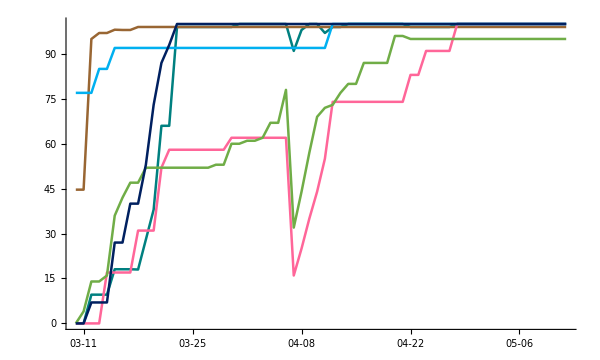

```mathematica
thickval=0.003;gratra=Show[Graphics[{colexp,Thickness[thickval],Line[data["Expressway"]]}],Graphics[{colroad,Thickness[thickval],Line[data["National road"]]}],Graphics[{colbul,Thickness[thickval],Line[data["Bullet train"]]}],Graphics[{coltrain,Thickness[thickval],Line[data["Local train"]]}],Graphics[{colair,Thickness[thickval],Line[data["Airport"]]}],Graphics[{colsea,Thickness[thickval],Line[data["Seaport"]]}],Axes->True,AxesOrigin->{-1,0},Ticks->{Table[{i,Rotate[ToString[datatemp⟦i,2⟧], 60 Degree]},{i,2,65,7}], Automatic},TicksStyle->Directive["Times",12],AspectRatio->.6,ImageSize->600]
```

```mathematica
Export["figure_transportation.png",gratra,"PNG"];
```